```mathematica
phig[r_,a0_,w0_,r0_]:= a0*(r/w0)^2*Exp[-((r-r0)/w0)^2]
```

```mathematica
bump[r_,rl_,ru_]:= (r-rl)^2*(r-ru)^2*Exp[-1/(ru - r) - 1/(r-rl) ]
```

```mathematica
phibump[r_,a0_,rl_,ru_]:= a0*bump[r,rl,ru]/bump[(rl+ru)/2,rl,ru]
```

```mathematica
r0=20.;
w0 = 10.;
rl = 8;
ru = 40;
```

General::munfl: Exp[-1529.75] is too small to represent as a normalized machine number; precision may be lost.

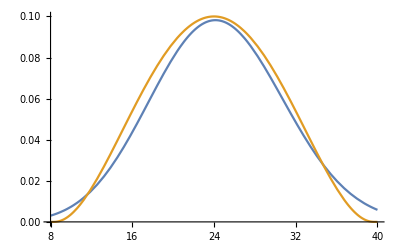

```mathematica
Plot[{phig[r,0.02,w0,r0], phibump[r,0.1,rl,ru]},{r,8,40}]
```

```mathematica
Quit
```

```mathematica
D[phig[r,a0,w0,r0],r]//Simplify;
Solve[%==0,r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→0},{r→1/2 (r0-√(r0^2+4 w0^2))},{r→1/2 (r0+√(r0^2+4 w0^2))}}

```mathematica
1/2 (r0+√(r0^2+4 w0^2))/.{r0-> 20,w0-> 10}//N
```

24.1421